```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

```mathematica
rain={0,2.602643312530441,1.3458908181542324,0.9786602954090866,0.4545766440470834,0.676163042182078,0.5858979580792466,1.780173188172434,0.8754892033856505,1.6056654237265842,1.8116246020010855,0,0.3433774351911117,2.3056477739965553,0.22590870432424015,0,0,0.0505596826937425,0,0,0.008287743798677472,0.14685356313718784,0.6632242738956761,0,0,1.19902505990126,1.0864416181527154,0.03820805023453355,1.3972017914558388,0,1.7781017183985999,3.039874652625664,4.752551163814718,2.7487873197896207,2.1848992374647573,1.6898070092856414,1.7572237690038426,0.9210565389605095,0.8798577188194684,1.405674033297716,0.8593950413685687,0.1548610040295721,0,0.803128246156472,0,0,0.4443343850224646,0,0,0.19495627895958723,1.0303566250921041,1.5060380213700335,1.8776085455049434,1.0218522879163947,1.1040194379800612,2.091970259438136,2.3119250069211956,1.601353394714088,0,0,0,0.080917812007125,0.8343110398520945,0.34855159245513195,0.0410498805239195,0.09275936292709935,0,0.0215223707983517,0,0,0,0,0,0,0,0.9761864121070692,0.13821943122303676,0,0.5527146222151169,1.9753226492574207,2.62421572641167,2.2223606695535794,2.8588785363899816,1.1140898137926027,0.5976927651918369,0.961361506670672,0.9407031547242389,0,0.4946430097949919,0,0.41462609161462266,0.6485890215604861,1.1368718051493785,0,2.3345557323672965,1.1047160918146637,1.1204724264670545,2.253916607007769,2.041303730274357,2.7323168706949703};
```

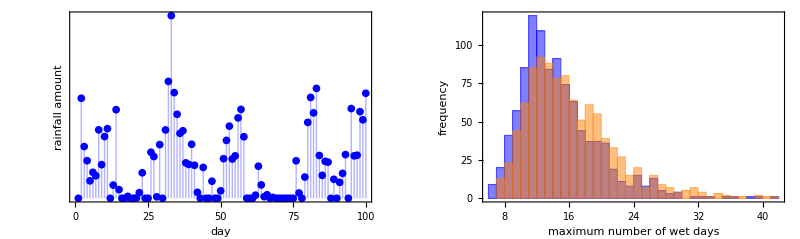

```mathematica
(*rain=RandomFunction[ARProcess[0.3,{.4,.2},1],{1,100}];
rain = Normal@rain;
rain = Flatten[rain,1][[All,2]];
rain = If[#<0,0,#]&/@rain;*)
wet = If[#==0,1,2]&/@rain;
wetVwet=MovingMap[If[#[[1]]>0&&#[[2]]>0,3,If[#[[1]]>0,2,1]]&,rain,2];
fWetSimple[nIterations_Integer,rain__,wet__]:=Module[{},ParallelTable[Max@(Length/@Cases[Split[Flatten[Normal@RandomFunction[EstimatedProcess[wet,DiscreteMarkovProcess[2]],{0,100}],1][[All,2]]],{2,__}]),{nIterations}]]
fWetComplex[nIterations_Integer,rain__,wetVwet__]:=Module[{},ParallelTable[Max@(Length/@Cases[Split[If[#>1,1,0]&/@Flatten[Normal@RandomFunction[EstimatedProcess[wetVwet,DiscreteMarkovProcess[3]],{0,100}],1][[All,2]]],{1,__}]),{nIterations}]]
(*Max@(Length/@Cases[Split[wet],{2,__}])*)
g1=ListPlot[rain,Filling->Axis,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"day","rainfall amount"},FrameTicks->{True,None},BaseStyle->{FontSize->16}];
g2=Histogram[{fWetSimple[1000,rain,wet],fWetComplex[1000,rain,wetVwet]},50,ChartStyle->{Blue,Orange},Frame->{True,True,False,False},FrameLabel->{"maximum number of wet days","frequency"},BaseStyle->{FontSize->16}];
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Evaluation_sensitivityRainfall.pdf",gFinal]
```

Evaluation_sensitivityRainfall.pdf